```mathematica
ClearAll["Global`*"]
```

```mathematica
namespace = StringJoin[{$HomeDirectory,"/PATH TO FOLDER/2024_PredSizeDiet"}];
```

```mathematica
eqnP = (w*bPred1*P*H1 +(1-w)* bPred2*P*H2) - μPred*P/.{bPred1->bPred1[Mp],bPred2->bPred2[Mp],μPred->μPred[Mp]}; (*,σPred->σPred[M],kC->kCons[M],Sub->Sub[M]*)
eqnH1 = λ1*(R/(k/2+R))*H1-( σ1*(1-R/k)+μ1+w*bmort1*P)*H1/.{k->kRes,λ1->λ1[Mp],μ1->μ1[Mp],σ1->σ1[Mp],bmort1->bmort1[Mp]};
eqnH2 = λ2*(R/(k/2+R))*H2-( σ2*(1-R/k)+μ2+(1-w)*bmort2*P)*H2/.{k->kRes,λ2->λ2[Mp],μ2->μ2[Mp],σ2->σ2[Mp],bmort2->bmort2[Mp]};
eqnR = α*R*(1-R/(k))-( λ1/Y1*(R/(k/2+R)))*H1-( λ2/Y2*(R/(k/2+R)))*H2/.{k->kRes,λ1->λ1[Mp],Y1->Y1[Mp],λ2->λ2[Mp],Y2->Y2[Mp]};
```

```mathematica
LVSS = FullSimplify[Solve[{0==eqnP,0==eqnH1,0==eqnH2,0==eqnR},{P,H1,H2,R}]];
```

```mathematica
Length[LVSS]
```

14

```mathematica
(*Internal Fixed Point*)
Psol = P/.LVSS[[13]];
H1sol = H1/.LVSS[[13]];
H2sol=H2/.LVSS[[13]];
Rsol = R/.LVSS[[13]];
```

What are the solutions if the predator is specializing on C1? (w->1)

```mathematica
PsolNoH2= FullSimplify[Psol/.w->1];
H1solNoH2= FullSimplify[H1sol/.w->1];
H2solNoH2= FullSimplify[H2sol/.w->1];
RsolNoH2 = FullSimplify[Rsol/.w->1];
```

```mathematica
JacobianGeneral=({
{D[eqnP,P],D[eqnP,H1],D[eqnP,H2],D[eqnP,R]},
{D[eqnH1,P],D[eqnH1,H1],D[eqnH1,H2],D[eqnH1,R]},
{D[eqnH2,P],D[eqnH2,H1],D[eqnH2,H2],D[eqnH2,R]},
{D[eqnR,P],D[eqnR,H1],D[eqnR,H2],D[eqnR,R]}});
```

```mathematica
JacobianFullModel=({
{D[eqnP,P],D[eqnP,H1],D[eqnP,H2],D[eqnP,R]},
{D[eqnH1,P],D[eqnH1,H1],D[eqnH1,H2],D[eqnH1,R]},
{D[eqnH2,P],D[eqnH2,H1],D[eqnH2,H2],D[eqnH2,R]},
{D[eqnR,P],D[eqnR,H1],D[eqnR,H2],D[eqnR,R]}})/.{P->Psol,H1->H1sol,H2->H2sol,R->Rsol};
```

```mathematica
data = Import[StringJoin[{namespace,"/data/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{namespace,"/data/carnivoredensities_trimmed.csv"}],"csv"];
```

***Declare Metabolic Parameters***

```mathematica
NotebookEvaluate[StringJoin[{namespace,"/src/metabolic_constants.nb"}]];
```

***Declare Allometric Functions - SPECIFIC TO MODEL AND PERSPECTIVE***

```mathematica
NotebookEvaluate[StringJoin[{namespace,"/src/allometric_functions_predpersp.nb"}]];
```

***Declare PPMR***

```mathematica
NotebookEvaluate[StringJoin[{namespace,"/src/ppmr_primary.nb"}]];
```

***Declare Analysis Functions***

```mathematica
NotebookEvaluate[StringJoin[{namespace,"/src/analysis_functions.nb"}]];
```

Show the inputted PPMR

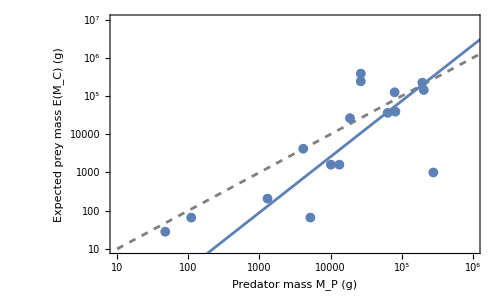

```mathematica
pstyleherb=Graphics[{EdgeForm[{Black,Thickness[0.2],Opacity[0.2]}],Opacity[0.1],FaceForm[Black],Disk[]}];
PPMRPlotLM = Show[{
ListLogLogPlot[ExpPreymassdata*1000,Frame->True,FrameLabel->{"Predator mass M_P (g)","Expected prey mass E(M_C) (g)"},LabelStyle->Directive[FontSize->16],PlotRange->{{10^1,1*10^6},{10^1,10^7}}],
ListLogLogPlot[Transpose[{Table[10^i,{i,1,7}],Table[10^i,{i,1,7}]}],Joined->True,PlotStyle->Directive[Gray,Dashed]],
ListLogLogPlot[ExpPreymassdata*1000,PlotMarkers->{Automatic,Medium}],
LogLogPlot[OptPreyMass[Mp],{Mp,10^1,10^7},PlotStyle->ColorData[97,1]]
},ImageSize->500,AspectRatio->3/5]
```

```mathematica
(*Export[StringJoin[{namespace,"/figures/fig_ppmr.pdf"}],PPMRPlotLM]*)
```

Check Original Model w/o predation... do we get pretty close to the Damuth Data without predation?
1/19/2023 - mass Coordinates for C2 are now converted to M2 units in the plot (where M2 = M1/ϕ)... so instead of a particular feature on the C2 curve relating to the mass of consumer 1, it now relates to the mass of consumer 2. So the x-axis is just ‘Consumer mass’, each C1 and C2 curve relating to M1 and M2, respectively.

```mathematica
PercentGrowthHerbivore1=0.9; (*Percent with which the predator relies on Herbivore 1 for food*)
ScaledMassHerbivore2 =0.9; (*Proportional size of Consumer 2 with respect to Herbivore 1 (focal)*)
H1DensityList=ParallelTable[{10^i,((1/OptPreyMass[Mp])*H1sol/.{w->PercentGrowthHerbivore1,ϕ->ScaledMassHerbivore2})/.Mp->10^i},{i,1,8,0.01}];
H1DensityListHerbMass = Transpose[{OptPreyMass[ H1DensityList[[All,1]]],H1DensityList[[All,2]]}];
H2DensityList=ParallelTable[{10^i,((1/(ϕ*OptPreyMass[Mp]))*H2sol/.{w->PercentGrowthHerbivore1,ϕ->ScaledMassHerbivore2})/.Mp->10^i},{i,1,8,0.01}];
H2DensityListHerbMass = Transpose[{OptPreyMass[ ϕ*H2DensityList[[All,1]]],H2DensityList[[All,2]]}];
```

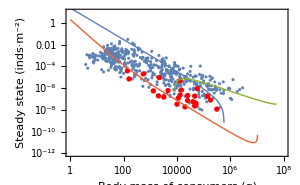

```mathematica
InternalPlot=Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-12,10}},Frame->True,FrameLabel->{"Body mass of consumers (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
ListLogLogPlot[H1DensityListHerbMass,Joined->True,PlotStyle->Directive[{Thick,ColorData[97,1]}]],
ListLogLogPlot[H2DensityListHerbMass/.ϕ->ScaledMassHerbivore2,Joined->True,PlotStyle->Directive[{Thick,ColorData[97,3]}]],
LogLogPlot[(1/Mp)*Psol/.{w->PercentGrowthHerbivore1,ϕ->ScaledMassHerbivore2},{Mp,1,10^8},Frame->True,PlotStyle->Directive[{Thick,ColorData[97,4]}]]
},ImageSize->300]
```

Detect population thresholds, where the density plummets to zero

Allow w and ϕ to vary, and calculate:
1) The C1 threshold mass (if it exists)
2) The C2 threshold mass (if it exists)
3) The difference in mass from C2 to C1 where 3 populations co-exist (if it exists)

FP Analysis
Analysis: Search for the stable steady state at each value of Mp, w, phi, and save P*,H1*,H2*,R* for that steady state

```mathematica
massexpvalues = Table[i,{i,4,7,0.1}];
wvalues = Table[i,{i,0.05,0.95,0.02}];
phivalues = Table[i,{i,0.05,2,0.02}];
```

```mathematica
(*StableFP = ParallelTable[
PredMass = 10^i;
If[phivalue != 1,
FPAnalysis[PredMass,wvalue,phivalue,JacobianGeneral,LVSS],
{PredMass,wvalue,phivalue,{Missing[],Missing[],Missing[],Missing[]},{Missing[],Missing[],Missing[],Missing[]},Missing[]}
],
{i,massexpvalues},{wvalue,wvalues},{phivalue,phivalues}
];
Export[StringJoin[{namespace,"/data/fixedpointwsPH1H2overWPhi.m"}],StableFP];*)
```

***
IMPORT SIMULATION RESULTS - The above code  ^^ takes 2-3 hours across 18 processors 
***

```mathematica
StableFP = Import[StringJoin[{namespace,"/data/fixedpointwsPH1H2overWPhi.m"}]];
```

Richness analysis - how many species are non-zero across w and phi?

```mathematica
RichnessArray=Table[
PredMass =i;
MassPos =Flatten[Position[Flatten[StableFP,2][[All,1]],PredMass],1];
wTable = Flatten[StableFP,2][[MassPos,2]];
phiTable = Flatten[StableFP,2][[MassPos,3]];
PdensTable =  Flatten[StableFP,2][[MassPos,4]][[All,1]];
H1densTable =  Flatten[StableFP,2][[MassPos,4]][[All,2]];
H2densTable =  Flatten[StableFP,2][[MassPos,4]][[All,3]];
SpRichness = Map[nonzeroQ,PdensTable]+Map[nonzeroQ,H1densTable]+Map[nonzeroQ,H2densTable];
SpRichness[[1]]=0;SpRichness[[2]]=1;SpRichness[[3]]=2;SpRichness[[4]]=3;
ListDensityPlot[Transpose[{wTable,phiTable,SpRichness}],InterpolationOrder->1,Mesh->None,ColorFunction->{ColorData[97,1],ColorData[97,2],ColorData[97,3],ColorData[97,4]},PlotLegends->SwatchLegend[{ColorData[97,1],ColorData[97,2],ColorData[97,3],ColorData[97,4]},{0,1,2,3},LegendLabel->"Richness"],PlotRange->Automatic,FrameLabel->{"w","ϕ"},FrameStyle->Thickness[0.01]],
{i,{10000.,100000.,1000000.}}];
RichnessPlot = GraphicsRow[RichnessArray,ImageSize->700,Spacings->0]
```

-Graphics-

Community analysis - Which species are present? This is a more complete analysis than the one above ^^

```mathematica
CommArray=Table[
Massvec = {10000.,100000.,1000000.};
i = Massvec[[j]];
PredMass =i;
MassPos =Flatten[Position[Flatten[StableFP,2][[All,1]],PredMass],1];
wTable = Flatten[StableFP,2][[MassPos,2]];
phiTable = Flatten[StableFP,2][[MassPos,3]];
PdensTable =  Flatten[StableFP,2][[MassPos,4]][[All,1]];
H1densTable =  Flatten[StableFP,2][[MassPos,4]][[All,2]];
H2densTable =  Flatten[StableFP,2][[MassPos,4]][[All,3]];

CommCode = ConstantArray[Missing[],Length[H1densTable]];
(*C1 Alone = 1*)
posH1 = Flatten[Position[Thread[{PdensTable,H1densTable,H2densTable}],{0|0.,_?(#>0&),0|0.}],1];
CommCode[[posH1]] = 1;
(*C2 Alone = 2*)
posH2 =Flatten[Position[Thread[{PdensTable,H1densTable,H2densTable}],{0|0.,0|0.,_?(#>0&)}],1];
CommCode[[posH2]] = 2;
(*C1 and C2 = 3*) (*NEVER HAPPENS*)
(*posC1C2 = Flatten[Position[Thread[{PdensTable,C1densTable,C2densTable}],{0|0.,_?(#>0&),_?(#>0&)}],1];
CommCode[[posC1C2]] = 3;*)
(*P and C1 = 4*)
posPH1 = Flatten[Position[Thread[{PdensTable,H1densTable,H2densTable}],{_?(#>0&),_?(#>0&),0|0.}],1];
CommCode[[posPH1]] = 3;
(*P and C2 = 5*)
posPH2=Flatten[Position[Thread[{PdensTable,H1densTable,H2densTable}],{_?(#>0&),0|0.,_?(#>0&)}],1];
CommCode[[posPH2]] = 4;
(*P and C1 and C2 = 6*)
posPH1H2=Flatten[Position[Thread[{PdensTable,H1densTable,H2densTable}],{_?(#>0&),_?(#>0&),_?(#>0&)}],1];
CommCode[[posPH1H2]] = 5;

(*CommCode[[1]]=1;CommCode[[2]]=2;CommCode[[3]]=3;CommCode[[4]]=4; CommCode[[5]]=5;*)

Codes = {"H_1","H_2","P+H_1","P+H_2","All"};
Masses={"M_P=10^4 g","M_P=10^5 g","M_P=10^6 g"};

UniqueIDs = DeleteCases[Sort[Flatten[UniqueElements[{CommCode}],1]],Missing[]];

ColorPalette = {ColorData[97,1],ColorData[97,3],ColorData[97,5],ColorData[97,2],ColorData[97,4]};
(*ColorPalette = Table[ColorData[98,i],{i,UniqueIDs}];*)

ListDensityPlot[Transpose[{wTable,phiTable,CommCode}],InterpolationOrder->1,Mesh->None,ColorFunction->Table[ColorPalette[[i]],{i,UniqueIDs}],PlotLegends->SwatchLegend[Table[ColorPalette[[i]],{i,UniqueIDs}],Table[Codes[[i]],{i,UniqueIDs}](*,LegendLabel->"Comm ID"*)],PlotRange->Automatic,FrameLabel->{"Prop. contribution of H_1, w_1","Relative mass of H_2, ϕ",Masses[[j]]},LabelStyle->Directive[FontSize->20,Black],ImageSize->300,FrameStyle->Directive[{Black,Thickness[0.003]}]],
{j,{1,2,3}}];
CommPlot = GraphicsRow[CommArray,ImageSize->1100,Spacings->0]
```

-Graphics-

```mathematica
Table[ColorData[98,i],{i,5}]
```

{RGBColor[0.29, 0.588, 0.612],RGBColor[0.886243, 0.527215, 0.0910023],RGBColor[0.613966, 0.37652, 0.585084],RGBColor[0.521981, 0.66, 0.0942065],RGBColor[0.820916, 0.341417, 0.22514]}

```mathematica
{ColorData[97,1],ColorData[97,3],ColorData[97,5],ColorData[97,2],ColorData[97,4]}
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.922526, 0.385626, 0.209179]}

```mathematica
massexpvalues = Table[i,{i,4,7,0.1}];
wvalues = Table[i,{i,0.05,0.95,0.02}];
phivalues = Table[i,{i,0.05,2,0.02}];
PropFeasible=Table[
PredMass = 10^massexpvalues[[i]];
MassPos =Flatten[Position[Flatten[StableFP,2][[All,1]],PredMass],1];
PdensTable =  Flatten[StableFP,2][[MassPos,4]][[All,1]];
H1densTable = Flatten[StableFP,2][[MassPos,4]][[All,2]];
H2densTable = Flatten[StableFP,2][[MassPos,4]][[All,3]];
PzeroPos =Flatten[Position[PdensTable,0|0.],1];
H1zeroPos =Flatten[Position[H1densTable,0|0.],1];
H2zeroPos =Flatten[Position[H2densTable,0|0.],1];
{
{PredMass,N[1 - Length[PzeroPos]/Length[PdensTable]]},
{PredMass,N[1 - Length[H1zeroPos]/Length[H1densTable]]},
{PredMass,N[1 - Length[H2zeroPos]/Length[H2densTable]]}
},
{i,1,Length[massexpvalues]}
];
```

```mathematica
PropCoexistence=Table[
PredMass = 10^massexpvalues[[i]];
MassPos =Flatten[Position[Flatten[StableFP,2][[All,1]],PredMass],1];
PdensTable =  Flatten[StableFP,2][[MassPos,4]][[All,1]];
H1densTable = Flatten[StableFP,2][[MassPos,4]][[All,2]];
H2densTable = Flatten[StableFP,2][[MassPos,4]][[All,3]];
(*Assume threshold is set.Replace'thresholdValue' with your actual threshold.*)
thresholdValue=10^-10;
(*Zip the two lists together*)
combinedList=Transpose[{H1densTable,H2densTable}];
combinedListAll=Transpose[{H1densTable,H2densTable,PdensTable}];

(*Use'Map' to apply the function to each pair of elements*)
coexistencePoints=Map[#[[1]]>thresholdValue&&#[[2]]>thresholdValue&,combinedList];
coexistencePointsAll=Map[#[[1]]>thresholdValue&&#[[2]]>thresholdValue&&#[[3]]>thresholdValue&,combinedListAll];

(*Calculate the proportion of coexistence*)
proportionOfCoexistence=Count[coexistencePoints,True]/Length[coexistencePoints];
proportionOfCoexistenceAll=Count[coexistencePointsAll,True]/Length[coexistencePointsAll];

{PredMass,proportionOfCoexistenceAll},
{i,1,Length[massexpvalues]}
];
```

```mathematica
interpFunc=Interpolation[PropCoexistence];
```

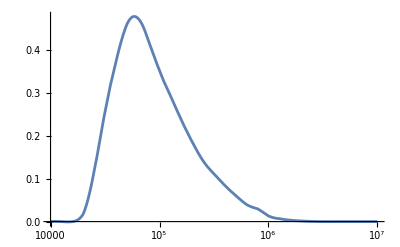

```mathematica
LogLinearPlot[interpFunc[M],{M,10^4,10^7}]
```

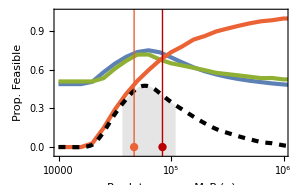

```mathematica
PropFeasiblePlot = 
Show[{
ListLogLinearPlot[PropFeasible[[All,2]],PlotRange->{{10^4,10^6},{-0.05,1.05}},Frame->True,FrameLabel->{"Predator mass, M_P (g)","Prop. Feasible"},PlotStyle->Directive[{Thickness[0.01],ColorData[97,1]}],Joined->True,LabelStyle->Directive[FontSize->20,Black],FrameStyle->Directive[{Black,Thickness[0.003]}]],
(*Graphics[{Red,Rectangle[{Log@(4.3*10^4),-1},{Log@(8.4*10^4),0.5}]}],*)
ListLogLinearPlot[PropFeasible[[All,3]],PlotStyle->Directive[{Thickness[0.01],ColorData[97,3]}],Joined->True],
ListLogLinearPlot[PropFeasible[[All,1]],PlotStyle->Directive[{Thickness[0.01],ColorData[97,4]}],Joined->True],
(*pointA =Log@(4.3*10^4);
pointB=Log@(8.4*10^4);*)
(*ListLogLinearPlot[PropCoexistence,PlotStyle->Directive[{Thickness[0.01],Black,Dashed}],Joined->True],*)
LogLinearPlot[interpFunc[M],{M,10^4,10^7},PlotStyle->Directive[{Thickness[0.01],Black,Dashed}]],
LogLinearPlot[interpFunc[M],{M,3.7*10^4,1.1*10^5},Filling->-1,FillingStyle->Directive[Opacity[0.1],Black],PlotStyle->Transparent],
Graphics[{PointSize[0.02],ColorData[97,4],Point[{Log@(4.7*10^4),0}]}],
Graphics[{PointSize[0.02],ColorData[97,4],Line[{{Log@(4.7*10^4),-0.99},{Log@(4.7*10^4),2}}]}],
Graphics[{PointSize[0.02],ColorData[85,1],Point[{Log@(8.4*10^4),0}]}],
Graphics[{PointSize[0.02],ColorData[85,1],Line[{{Log@(8.4*10^4),-0.99},{Log@(8.4*10^4),2}}]}]

},ImageSize->300]
```

```mathematica
maxPair=MaximalBy[PropCoexistence,Last]
```

{{63095.7,533/1127}}

Fixed Point analysis to show higher resolution densities as a function of Mp for a GIVEN w and phi value

```mathematica
massexpvalues = Table[i,{i,1,8,0.01}];
wvalue = 0.8;
phivalue= 0.8;
(*wvalues = Table[i,{i,0.1,0.9,0.1}];
phivalues = Table[i,{i,0.1,2,0.1}];*)
StableFPSpecific = ParallelTable[
PredMass = 10^i;
If[phivalue != 1,
FPResults = FPAnalysis[PredMass,wvalue,phivalue,JacobianGeneral,LVSS];
{FPResults[[1]],FPResults[[4]],FPResults[[5]],FPResults[[6]]},
{PredMass,{Missing[],Missing[],Missing[],Missing[]},{Missing[],Missing[],Missing[],Missing[]},Missing[]}
],
{i,massexpvalues}
];
(*Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2024_PCR/data/fixedpointwsPC1C2overWPhi_HaywardLogit3.m"}],StableFP];*)
```

Remember - we have to convert Mass values (= predator mass values) to 1) C1 mass values and 2) C2 mass values

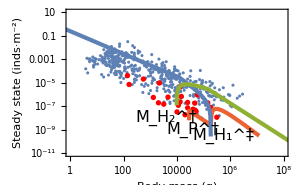

```mathematica
Pdensities=Transpose[{StableFPSpecific[[All,1]],StableFPSpecific[[All,2]][[All,1]]}];
H1densities=Transpose[{OptPreyMass[StableFPSpecific[[All,1]]],Re[StableFPSpecific[[All,2]][[All,2]]]}];
H2densities=Transpose[{OptPreyMass[StableFPSpecific[[All,1]]]*phivalue,Re[StableFPSpecific[[All,2]][[All,3]]]}];
InternalStablePlot=Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,10}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->20,Black],FrameStyle->Directive[{Black,Thickness[0.003]}]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
ListLogLogPlot[Pdensities,Joined->True,PlotStyle->Directive[{Thickness[0.01],ColorData[97,4]}],PlotRange->{{1,10^8},{10^-12,1}}],
ListLogLogPlot[H1densities,Joined->True,PlotStyle->Directive[{Thickness[0.01],ColorData[97,1]}]],
ListLogLogPlot[H2densities,Joined->True,PlotStyle->Directive[{Thickness[0.01],ColorData[97,3]}]],
Graphics[{Text[Style["M_P^†",FontSize->16],{Log@(10^4.6),Log@(10^(-9.0))}]}],
Graphics[{Text[Style["M_H_1^‡",FontSize->16],{Log@(10^5.75),Log@(10^(-9.5))}]}],
Graphics[{Text[Style["M_H_2^†",FontSize->16],{Log@(10^3.6),Log@(10^(-8.0))}]}]
},ImageSize->300]
```

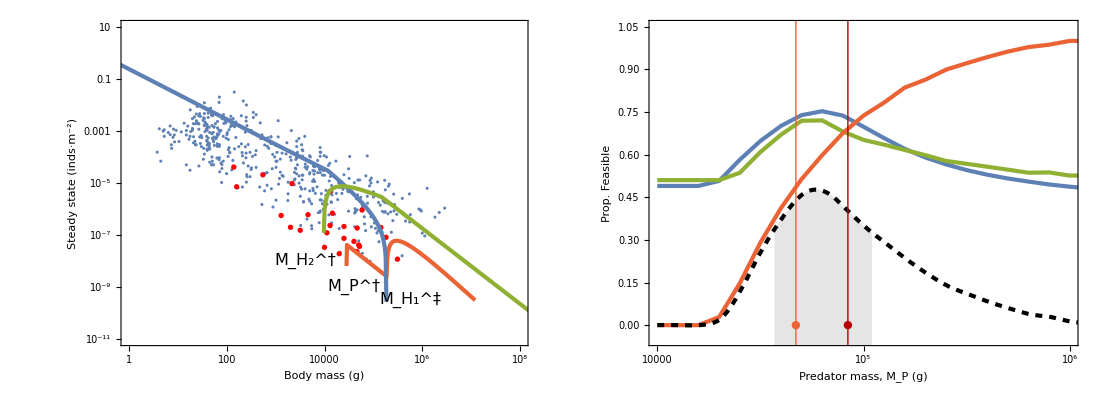

```mathematica
DensityFeasibilityPlot = GraphicsRow[{InternalStablePlot,PropFeasiblePlot},ImageSize->1100,Spacings->0]
```

```mathematica
CombinedDensityCommPlot = GraphicsColumn[{
DensityFeasibilityPlot,
CommPlot
},ImageSize->1200,Spacings->0]
```

-Graphics-

```mathematica
Export[StringJoin[{namespace,"/final_figures/fig_propfeasible_Comm2.png"}],CombinedDensityCommPlot,ImageResolution->800]
```

Predator density analysis at 10^5 and 10^6 grams - This plot captures the changing roles of generalization (w=0.5) for macro- and megapredators

```mathematica
PredMass0 =10^4.5;
MassPos0 =Flatten[Position[Flatten[StableFP,2][[All,1]],PredMass0],1];
wTable0 = Flatten[StableFP,2][[MassPos0,2]];
phiTable0 = Flatten[StableFP,2][[MassPos0,3]];
PdensTable0 =  Flatten[StableFP,2][[MassPos0,4]][[All,1]];
PzeroPos0 =Flatten[Position[PdensTable0,0|0.],1];
Pzeros0 = Transpose[{wTable0[[PzeroPos0]],phiTable0[[PzeroPos0]]}];

PredMass1 =10^4.7;
MassPos1 =Flatten[Position[Flatten[StableFP,2][[All,1]],PredMass1],1];
wTable1 = Flatten[StableFP,2][[MassPos1,2]];
phiTable1 = Flatten[StableFP,2][[MassPos1,3]];
PdensTable1 =  Flatten[StableFP,2][[MassPos1,4]][[All,1]];
PzeroPos1 =Flatten[Position[PdensTable1,0|0.],1];
Pzeros1 = Transpose[{wTable1[[PzeroPos1]],phiTable1[[PzeroPos1]]}];

PredMass2 =10^5.;
MassPos2 =Flatten[Position[Flatten[StableFP,2][[All,1]],PredMass2],1];
wTable2 = Flatten[StableFP,2][[MassPos2,2]];
phiTable2 = Flatten[StableFP,2][[MassPos2,3]];
PdensTable2 =  Flatten[StableFP,2][[MassPos2,4]][[All,1]];
PzeroPos2 =Flatten[Position[PdensTable2,0|0.],1];
Pzeros2 = Transpose[{wTable2[[PzeroPos2]],phiTable2[[PzeroPos2]]}];

PredMass2b =10^5.2;
MassPos2b =Flatten[Position[Flatten[StableFP,2][[All,1]],PredMass2b],1];
wTable2b = Flatten[StableFP,2][[MassPos2b,2]];
phiTable2b = Flatten[StableFP,2][[MassPos2b,3]];
PdensTable2b =  Flatten[StableFP,2][[MassPos2b,4]][[All,1]];
PzeroPos2b =Flatten[Position[PdensTable2b,0|0.],1];
Pzeros2b = Transpose[{wTable2b[[PzeroPos2b]],phiTable2b[[PzeroPos2b]]}];

PredMass3 =10^5.5;
MassPos3 =Flatten[Position[Flatten[StableFP,2][[All,1]],PredMass3],1];
wTable3 = Flatten[StableFP,2][[MassPos3,2]];
phiTable3 = Flatten[StableFP,2][[MassPos3,3]];
PdensTable3 =  Flatten[StableFP,2][[MassPos3,4]][[All,1]];
PzeroPos3 =Flatten[Position[PdensTable3,0|0.],1];
Pzeros3 = Transpose[{wTable3[[PzeroPos3]],phiTable3[[PzeroPos3]]}];

PredMass4 =10^6.;
MassPos4 =Flatten[Position[Flatten[StableFP,2][[All,1]],PredMass4],1];
wTable4 = Flatten[StableFP,2][[MassPos4,2]];
phiTable4 = Flatten[StableFP,2][[MassPos4,3]];
PdensTable4 =  Flatten[StableFP,2][[MassPos4,4]][[All,1]];
(*PzeroPos2 =Flatten[Position[PdensTable2,0|0.],1];
Pzeros2 = Transpose[{wTable2[[PzeroPos2]],phiTable2[[PzeroPos2]]}];*)
PredDensityPlot4MTop=GraphicsRow[{
Show[{
ListContourPlot[Transpose[{wTable0,phiTable0,PdensTable0}],PlotRange->{0,All},PlotLegends->BarLegend[Automatic,LegendLabel->"P dens"],FrameLabel->{"Prop. contribution of C_1, w","Rel. mass of C_2, ϕ=M_2/M_1",StringJoin[{"M_P=10^4.5 g"}] },Contours->50,ContourStyle->None,LabelStyle->Directive[FontSize->16]],
Graphics[{White,Opacity[1],ConcaveHullMesh[Pzeros0,0.02,All]}]
},ImageSize->250],
Show[{
ListContourPlot[Transpose[{wTable1,phiTable1,PdensTable1}],PlotRange->{0,All},PlotLegends->BarLegend[Automatic,LegendLabel->"P dens"],FrameLabel->{"Prop. contribution of C_1, w","Rel. mass of C_2, ϕ=M_2/M_1",StringJoin[{"M_P=10^4.7 g"}] },Contours->50,ContourStyle->None,LabelStyle->Directive[FontSize->16]]
,Graphics[{White,Opacity[1],ConcaveHullMesh[Pzeros1,0.02,All]}]
},ImageSize->250],
Show[{
ListContourPlot[Transpose[{wTable2,phiTable2,PdensTable2}],PlotRange->{0,All},PlotLegends->BarLegend[Automatic,LegendLabel->"P dens"],FrameLabel->{"Prop. contribution of C_1, w","Rel. mass of C_2, ϕ=M_2/M_1",StringJoin[{"M_P=10^5.0 g"}] },Contours->50,ContourStyle->None,LabelStyle->Directive[FontSize->16]],
Graphics[{White,Opacity[1],ConcaveHullMesh[Pzeros2,0.02,All]}]
},ImageSize->250]
}];
PredDensityPlot4MBottom=GraphicsRow[{
Show[{
ListContourPlot[Transpose[{wTable2b,phiTable2b,PdensTable2b}],PlotRange->{0,All},PlotLegends->BarLegend[Automatic,LegendLabel->"P dens"],FrameLabel->{"Prop. contribution of C_1, w","Rel. mass of C_2, ϕ=M_2/M_1",StringJoin[{"M_P=10^5.2 g"}] },Contours->50,ContourStyle->None,LabelStyle->Directive[FontSize->16]],
Graphics[{White,Opacity[1],ConcaveHullMesh[Pzeros2,0.02,All]}]
},ImageSize->250],
Show[{
ListContourPlot[Transpose[{wTable3,phiTable3,PdensTable3}],PlotRange->{0,All},PlotLegends->BarLegend[Automatic,LegendLabel->"P dens"],FrameLabel->{"Prop. contribution of C_1, w","Rel. mass of C_2, ϕ=M_2/M_1",StringJoin[{"M_P=10^5.5 g"}] },Contours->50,ContourStyle->None,LabelStyle->Directive[FontSize->16]],
Graphics[{White,Opacity[1],ConcaveHullMesh[Pzeros3,0.02,All]}]
},ImageSize->250],
Show[{
ListContourPlot[Transpose[{wTable4,phiTable4,PdensTable4}],PlotRange->{0,All},PlotLegends->BarLegend[Automatic,LegendLabel->"P dens"],FrameLabel->{"Prop. contribution of C_1, w","Rel. mass of C_2, ϕ=M_2/M_1",StringJoin[{"M_P=10^6.0 g"}] },Contours->50,ContourStyle->None,LabelStyle->Directive[FontSize->16]](*,
Graphics[{White,Opacity[1],ConcaveHullMesh[Pzeros2,0.02,All]}]*)
},ImageSize->250]
}];
PredDensityPlot4M=GraphicsColumn[{PredDensityPlot4MTop,PredDensityPlot4MBottom},ImageSize->1300,Spacings->0]
```

-Graphics-

Predator Generality Figure

```mathematica
massexpvalues = Table[i,{i,4,6,0.005}];
```

```mathematica
(*StableFPRatio = ParallelTable[
PredMass = 10^i;
If[phivalue != 1,
FPAnalysis[PredMass,wvalue,phivalue,JacobianGeneral,LVSS],
{PredMass,wvalue,phivalue,{Missing[],Missing[],Missing[],Missing[]},{Missing[],Missing[],Missing[],Missing[]},Missing[]}
],
{i,massexpvalues},{wvalue,{(*0.1,0.2,0.3,*)0.5,0.75,0.8,0.85,0.9}},{phivalue,{0.2,0.8,1.2}}
];
Export[StringJoin[{namespace,"/data/fixedpointwsPH1H2Ratio.m"}],StableFPRatio];*)
```

```mathematica
StableFPRatio=Import[StringJoin[{namespace,"/data/fixedpointwsPH1H2Ratio.m"}]];
```

```mathematica
wvaluegeneralist = 0.5;
wvaluespecialistsmall = 0.75;
(*wvaluespecialistlarge = 0.2;*)
wvaluespecialistsmallextreme = 0.85;
(*wvaluespecialistlargeextreme = 0.1;*)
phivaluesmall = 0.2;
phivaluelarge = 1.2;
GenWPos = Flatten[Position[Flatten[StableFPRatio,2][[All,2]],wvaluegeneralist],1];
PhiPosSmall = Flatten[Position[Flatten[StableFPRatio,2][[All,3]],phivaluesmall],1];
PhiPosLarge = Flatten[Position[Flatten[StableFPRatio,2][[All,3]],phivaluelarge],1];
SpecWPosSmall = Flatten[Position[Flatten[StableFPRatio,2][[All,2]],wvaluespecialistsmall],1];
(*SpecWPosLarge = Flatten[Position[Flatten[StableFPRatio,2][[All,2]],wvaluespecialistlarge],1];*)
SpecWPosSmallextreme = Flatten[Position[Flatten[StableFPRatio,2][[All,2]],wvaluespecialistsmallextreme],1];
(*SpecWPosLargeextreme = Flatten[Position[Flatten[StableFPRatio,2][[All,2]],wvaluespecialistlargeextreme],1];*)
(*w = 0.5; phi = 0.8; Generalist when C1 is larger and C2 is smaller*)
GenPosSmall = Intersection[GenWPos,PhiPosSmall];
(*w = 0.8; phi = 0.8; Specialist on larger C1 because C2 = 80% size of C1*)
SpecPosSmall = Intersection[SpecWPosSmall,PhiPosSmall];
SpecPosSmallextreme = Intersection[SpecWPosSmallextreme,PhiPosSmall];
(*w = 0.5; phi = 1.2; Generalist when C1 is smaller and C2 is larger*)
GenPosLarge = Intersection[GenWPos,PhiPosLarge];
(*w = 0.2; phi = 1.2; Specialist on smaller C2 and C2 = 120% size of C1*)
(*SpecPosLarge = Intersection[SpecWPosLarge,PhiPosLarge];
SpecPosLargeextreme = Intersection[SpecWPosLargeextreme,PhiPosLarge];*)
```

```mathematica
(*predatordiets = Import[StringJoin[{namespace,"/data/diet_results.csv"}],"CSV","HeaderLines"->1];*)
predatordiets = Import[StringJoin[{namespace,"/data/diet_results_rangearea.csv"}],"CSV","HeaderLines"->1];
sinclairdiets = Import[StringJoin[{namespace,"/data/diet_sinclair_results.csv"}],"CSV","HeaderLines"->1];
columnNames={"loc","time","carnivore","herb_range","herb_area","ratio","predmassmin","predmassmax","family","source","habitat","ratiotype"};
columnNamesSinclair={"loc","time","carnivore","herb_range","carn_range","ratio","predmassmin","predmassmax","family","source"};
predatordiets=Dataset[AssociationThread[columnNames->#]&/@predatordiets];
sinclairdiets=Dataset[AssociationThread[columnNamesSinclair->#]&/@sinclairdiets];
```

```mathematica
DataCanids=Select[predatordiets,#["ratio"]>0&&#["family"]=="C"&&#["predmassmin"]>20&];
(*Extract minMass,maxMass,and ratios for the filtered data*)
minMassCanids=DataCanids[All,"predmassmin"]//Normal;
maxMassCanids=DataCanids[All,"predmassmax"]//Normal;
ratiosCanids=DataCanids[All,"ratio"]//Normal;
(*Calculate the mean log mass for each predator*)
meanMassCanids=Table[Mean[{minMassCanids[[i]],maxMassCanids[[i]]}],{i,Length[minMassCanids]}];

DataCanidsModern=Select[sinclairdiets,#["ratio"]>0&&#["family"]=="C"&&#["predmassmin"]>20&];
minMassCanidsModern=DataCanidsModern[All,"predmassmin"]//Normal;
maxMassCanidsModern=DataCanidsModern[All,"predmassmax"]//Normal;
ratiosCanidsModern=DataCanidsModern[All,"ratio"]//Normal;
meanMassCanidsModern=Table[Mean[{minMassCanidsModern[[i]],maxMassCanidsModern[[i]]}],{i,Length[minMassCanidsModern]}];

DataFelids=Select[predatordiets,#["ratio"]>0&&#["family"]=="F"&&#["predmassmin"]>20&];
(*Extract minMass,maxMass,and ratios for the filtered data*)
minMassFelids=DataFelids[All,"predmassmin"]//Normal;
maxMassFelids=DataFelids[All,"predmassmax"]//Normal;
ratiosFelids=DataFelids[All,"ratio"]//Normal;
(*Calculate the mean log mass for each predator*)
meanMassFelids=Table[Mean[{minMassFelids[[i]],maxMassFelids[[i]]}],{i,Length[minMassFelids]}];

DataFelidsModern=Select[sinclairdiets,#["ratio"]>0&&#["family"]=="F"&&#["predmassmin"]>20&];
minMassFelidsModern=DataFelidsModern[All,"predmassmin"]//Normal;
maxMassFelidsModern=DataFelidsModern[All,"predmassmax"]//Normal;
ratiosFelidsModern=DataFelidsModern[All,"ratio"]//Normal;
meanMassFelidsModern=Table[Mean[{minMassFelidsModern[[i]],maxMassFelidsModern[[i]]}],{i,Length[minMassFelidsModern]}];

DataUrsids=Select[predatordiets,#["ratio"]>0&&#["family"]=="U"&&#["predmassmin"]>20&];
(*Extract minMass,maxMass,and ratios for the filtered data*)
minMassUrsids=DataUrsids[All,"predmassmin"]//Normal;
maxMassUrsids=DataUrsids[All,"predmassmax"]//Normal;
ratiosUrsids=DataUrsids[All,"ratio"]//Normal;
(*Calculate the mean log mass for each predator*)
meanMassUrsids=Table[Mean[{minMassUrsids[[i]],maxMassUrsids[[i]]}],{i,Length[minMassUrsids]}];

DataHyenids=Select[predatordiets,#["ratio"]>0&&#["family"]=="H"&&#["predmassmin"]>20&];
(*Extract minMass,maxMass,and ratios for the filtered data*)
minMassHyenids=DataHyenids[All,"predmassmin"]//Normal;
maxMassHyenids=DataHyenids[All,"predmassmax"]//Normal;
ratiosHyenids=DataHyenids[All,"ratio"]//Normal;
(*Calculate the mean log mass for each predator*)
meanMassHyenids=Table[Mean[{minMassHyenids[[i]],maxMassHyenids[[i]]}],{i,Length[minMassHyenids]}];

DataHyenidsModern=Select[sinclairdiets,#["ratio"]>0&&#["family"]=="H"&&#["predmassmin"]>20&];
minMassHyenidsModern=DataHyenidsModern[All,"predmassmin"]//Normal;
maxMassHyenidsModern=DataHyenidsModern[All,"predmassmax"]//Normal;
ratiosHyenidsModern=DataHyenidsModern[All,"ratio"]//Normal;
meanMassHyenidsModern=Table[Mean[{minMassHyenidsModern[[i]],maxMassHyenidsModern[[i]]}],{i,Length[minMassHyenidsModern]}];
```

Select datapoints for which we calculate the range (d13C only)

```mathematica
DataType=Select[predatordiets,#["ratio"]>0&&#["ratiotype"]=="range"&&#["predmassmin"]>20&];
minMassType = DataType[All,"predmassmin"]//Normal;
maxMassType = DataType[All,"predmassmax"]//Normal;
ratioType = DataType[All,"ratio"]//Normal;
meanMassType = Table[Mean[{minMassType[[i]],maxMassType[[i]]}],{i,Length[minMassType]}];
```

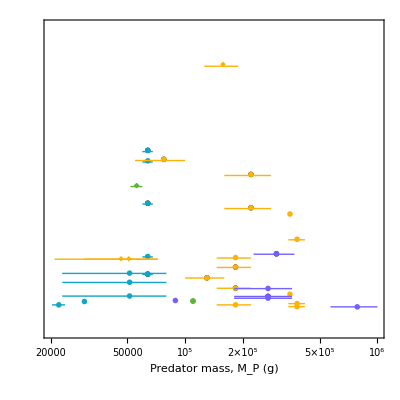

```mathematica
SmallScale = 0.04;
DiamondScale = 0.09;
ColorDataSet = 100;
baroffset = 0.008;
secondaryPlot=
Show[{
ListLogLinearPlot[Transpose[{meanMassType*1000,ratioType}],
Frame->True,FrameTicks->{{None,All},{Automatic,None}},FrameLabel->{{"","Relative diet breadth proxy"},{"Predator mass, M_P (g)",None}},PlotStyle->Black,
PlotMarkers->{"●",Scaled[0.06]},LabelStyle->Directive[FontSize->16,Black],PlotRange->{{2*10^4,10^6},{-0.1,1.15}},ImageSize->400,AspectRatio->1,ImagePadding->{{50,60},{60,40}}],

ListLogLinearPlot[Transpose[{meanMassCanids*1000,ratiosCanids}],
Frame->True,FrameTicks->{{None,All},{Automatic,None}},FrameLabel->{{"","Relative diet breadth proxy"},{"Predator mass, M_P (g)",None}},PlotStyle->ColorData[ColorDataSet,1],
PlotMarkers->{"●",Scaled[SmallScale]},LabelStyle->Directive[FontSize->16,Black],PlotRange->{{2*10^4,10^6},{-0.1,1.15}},ImageSize->400,AspectRatio->1,ImagePadding->{{50,60},{60,40}}],
Table[
Graphics[{ColorData[ColorDataSet,1],Line[{{Log@(minMassCanids[[i]]*1000),ratiosCanids[[i]]*(1-baroffset)},{Log@(maxMassCanids[[i]]*1000),ratiosCanids[[i]]*(1-baroffset)}}]}],
{i,1,Length[minMassCanids]}],

ListLogLinearPlot[Transpose[{meanMassCanidsModern*1000,ratiosCanidsModern}],
Frame->True,FrameTicks->{{None,All},{Automatic,None}},FrameLabel->{{"","Relative isotopic breadth"},{"Predator mass, M_P (g)",None}},PlotStyle->ColorData[ColorDataSet,1],
PlotMarkers->{"◆",Scaled[DiamondScale]},LabelStyle->Directive[FontSize->16],PlotRange->{{5*10^4,10^6},All},ImageSize->400,AspectRatio->1,ImagePadding->{{50,60},{60,40}}],
Table[
Graphics[{ColorData[ColorDataSet,1],Line[{{Log@(minMassCanidsModern[[i]]*1000),ratiosCanidsModern[[i]]*(1-baroffset)},{Log@(maxMassCanidsModern[[i]]*1000),ratiosCanidsModern[[i]]*(1-baroffset)}}]}],
{i,1,Length[minMassCanidsModern]}],

ListLogLinearPlot[Transpose[{meanMassFelids*1000,ratiosFelids}],
Frame->True,FrameTicks->{{None,All},{Automatic,None}},FrameLabel->{{"","Relative isotopic breadth"},{"Predator mass, M_P (g)",None}},PlotStyle->ColorData[ColorDataSet,2],
PlotMarkers->{"●",Scaled[SmallScale]},LabelStyle->Directive[FontSize->16],PlotRange->{{5*10^4,10^6},All},ImageSize->400,AspectRatio->1,ImagePadding->{{50,60},{60,40}}],
Table[
Graphics[{ColorData[ColorDataSet,2],Line[{{Log@(minMassFelids[[i]]*1000),ratiosFelids[[i]]*(1-baroffset)},{Log@(maxMassFelids[[i]]*1000),ratiosFelids[[i]]*(1-baroffset)}}]}],
{i,1,Length[minMassFelids]}],

ListLogLinearPlot[Transpose[{meanMassFelidsModern*1000,ratiosFelidsModern}],
Frame->True,FrameTicks->{{None,All},{Automatic,None}},FrameLabel->{{"","Relative isotopic breadth"},{"Predator mass, M_P (g)",None}},PlotStyle->ColorData[ColorDataSet,2],
PlotMarkers->{"◆",Scaled[DiamondScale]},LabelStyle->Directive[FontSize->16],PlotRange->{{5*10^4,10^6},All},ImageSize->400,AspectRatio->1,ImagePadding->{{50,60},{60,40}}],
Table[
Graphics[{ColorData[ColorDataSet,2],Line[{{Log@(minMassFelidsModern[[i]]*1000),ratiosFelidsModern[[i]]*(1-baroffset)},{Log@(maxMassFelidsModern[[i]]*1000),ratiosFelidsModern[[i]]*(1-baroffset)}}]}],
{i,1,Length[minMassFelidsModern]}],

ListLogLinearPlot[Transpose[{meanMassUrsids*1000,ratiosUrsids}],
Frame->True,FrameTicks->{{None,All},{Automatic,None}},FrameLabel->{{"","Relative isotopic breadth"},{"Predator mass, M_P (g)",None}},PlotStyle->ColorData[ColorDataSet,3],
PlotMarkers->{"●",Scaled[SmallScale]},LabelStyle->Directive[FontSize->16],PlotRange->{{5*10^4,10^6},All},ImageSize->400,AspectRatio->1,ImagePadding->{{50,60},{60,40}}],
Table[
Graphics[{ColorData[ColorDataSet,3],Line[{{Log@(minMassUrsids[[i]]*1000),ratiosUrsids[[i]]*(1-baroffset)},{Log@(maxMassUrsids[[i]]*1000),ratiosUrsids[[i]]*(1-baroffset)}}]}],
{i,1,Length[minMassUrsids]}],

ListLogLinearPlot[Transpose[{meanMassHyenids*1000,ratiosHyenids}],
Frame->True,FrameTicks->{{None,All},{Automatic,None}},FrameLabel->{{"","Relative isotopic breadth"},{"Predator mass, M_P (g)",None}},PlotStyle->ColorData[ColorDataSet,4],
PlotMarkers->{"●",Scaled[SmallScale]},LabelStyle->Directive[FontSize->16],PlotRange->{{5*10^4,10^6},All},ImageSize->400,AspectRatio->1,ImagePadding->{{50,60},{60,40}}],
Table[
Graphics[{ColorData[ColorDataSet,4],Line[{{Log@(minMassHyenids[[i]]*1000),ratiosHyenids[[i]]*(1-baroffset)},{Log@(maxMassHyenids[[i]]*1000),ratiosHyenids[[i]]*(1-baroffset)}}]}],
{i,1,Length[minMassHyenids]}],

ListLogLinearPlot[Transpose[{meanMassHyenidsModern*1000,ratiosHyenidsModern}],
Frame->True,FrameTicks->{{None,All},{Automatic,None}},FrameLabel->{{"","Relative isotopic breadth"},{"Predator mass, M_P (g)",None}},PlotStyle->ColorData[ColorDataSet,4],
PlotMarkers->{"◆",Scaled[DiamondScale]},LabelStyle->Directive[FontSize->16],PlotRange->{{5*10^4,10^6},All},ImageSize->400,AspectRatio->1,ImagePadding->{{50,60},{60,40}}],
Table[
Graphics[{ColorData[ColorDataSet,4],Line[{{Log@(minMassHyenidsModern[[i]]*1000),ratiosHyenidsModern[[i]]*(1-baroffset)},{Log@(maxMassHyenidsModern[[i]]*1000),ratiosHyenidsModern[[i]]*(1-baroffset)}}]}],
{i,1,Length[minMassHyenidsModern]}]
}]
```

{57544.,421697.}

{56885.3,668344.}

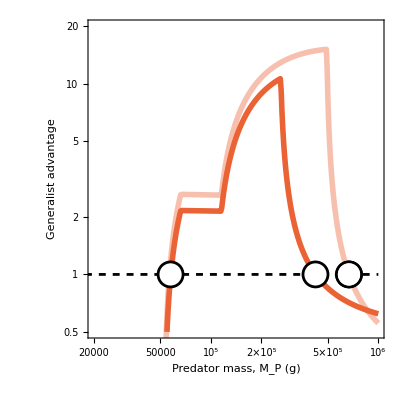

```mathematica
PDensitiesRatioSmall = Quiet[Transpose[{Flatten[StableFPRatio,2][[GenPosSmall,1]],((*1+*)Re[Flatten[StableFPRatio,2][[GenPosSmall,4]][[All,1]]])/((*1+*)Re[Flatten[StableFPRatio,2][[SpecPosSmall,4]][[All,1]]])}]];
(*PDensitiesRatioLarge = Quiet[Transpose[{Flatten[StableFPRatio,2][[GenPosLarge,1]],((*1+*)Re[Flatten[StableFPRatio,2][[GenPosLarge,4]][[All,1]]])/((*1+*)Re[Flatten[StableFPRatio,2][[SpecPosLarge,4]][[All,1]]])}]];*)
RealNumberRatioPosSmall = Flatten[Position[PDensitiesRatioSmall[[All,2]],_?(NumericQ[#]&&#>0&)],1];
(*RealNumberRatioPosLarge = Flatten[Position[PDensitiesRatioLarge[[All,2]],_?(NumericQ[#]&&#>0&)],1];*)

PDensitiesRatioSmallextreme = Quiet[Transpose[{Flatten[StableFPRatio,2][[GenPosSmall,1]],((*1+*)Re[Flatten[StableFPRatio,2][[GenPosSmall,4]][[All,1]]])/((*1+*)Re[Flatten[StableFPRatio,2][[SpecPosSmallextreme,4]][[All,1]]])}]];
(*PDensitiesRatioLargeextreme = Quiet[Transpose[{Flatten[StableFPRatio,2][[GenPosLarge,1]],((*1+*)Re[Flatten[StableFPRatio,2][[GenPosLarge,4]][[All,1]]])/((*1+*)Re[Flatten[StableFPRatio,2][[SpecPosLargeextreme,4]][[All,1]]])}]];*)
RealNumberRatioPosSmallextreme = Flatten[Position[PDensitiesRatioSmallextreme[[All,2]],_?(NumericQ[#]&&#>0&)],1];
(*RealNumberRatioPosLargeextreme = Flatten[Position[PDensitiesRatioLargeextreme[[All,2]],_?(NumericQ[#]&&#>0&)],1];*)

(*ISOLATE INTERCEPTS*)

(*Assuming PDensitiesRatioSmall[[RealNumberRatioPosSmall]] is your list of points*)
points=PDensitiesRatioSmall[[RealNumberRatioPosSmall]];

(*Define threshold x-value to separate the two regions*)
thresholdX=300000;  (*You can adjust this value based on your data distribution*)

(*Split points into two regions based on x-value*)
pointsRegion1=Select[points,#[[1]]<thresholdX&];
pointsRegion2=Select[points,#[[1]]>=thresholdX&];

(*Function to find the point closest to y=1 in a given region*)
findClosestPointToY1[regionPoints_]:=Module[{sortedPoints,closestPoint},sortedPoints=SortBy[regionPoints,Abs[#[[2]]-1]&];
closestPoint=First[sortedPoints];
closestPoint[[1]]  (*Return the x-coordinate of the closest point*)];

(*Find the closest points to y=1 in each region*)
xCoordinate1=findClosestPointToY1[pointsRegion1];
xCoordinate2=findClosestPointToY1[pointsRegion2];

(*Output the x-coordinates for the intersections*)
xinterceptsRatioSmall = {xCoordinate1,xCoordinate2};

(*Assuming PDensitiesRatioSmall[[RealNumberRatioPosSmall]] is your list of points*)
points=PDensitiesRatioSmallextreme[[RealNumberRatioPosSmallextreme]];

(*Define threshold x-value to separate the two regions*)
thresholdX=300000;  (*You can adjust this value based on your data distribution*)

(*Split points into two regions based on x-value*)
pointsRegion1=Select[points,#[[1]]<thresholdX&];
pointsRegion2=Select[points,#[[1]]>=thresholdX&];

(*Function to find the point closest to y=1 in a given region*)
findClosestPointToY1[regionPoints_]:=Module[{sortedPoints,closestPoint},sortedPoints=SortBy[regionPoints,Abs[#[[2]]-1]&];
closestPoint=First[sortedPoints];
closestPoint[[1]]  (*Return the x-coordinate of the closest point*)];

(*Find the closest points to y=1 in each region*)
xCoordinate1=findClosestPointToY1[pointsRegion1];
xCoordinate2=findClosestPointToY1[pointsRegion2];

(*Output the x-coordinates for the intersections*)
xinterceptsRatioSmallextreme = {xCoordinate1,xCoordinate2};

xinterceptsRatioSmall
xinterceptsRatioSmallextreme


DensityRatioPlot=Show[{
ListLogLogPlot[PDensitiesRatioSmall[[RealNumberRatioPosSmall]],Joined->True,PlotStyle->Directive[{Thickness[0.01],ColorData[97,4]}],Frame->True,FrameLabel->{"Predator mass, M_P (g)","Generalist advantage","ϕ=0.8"},LabelStyle->Directive[FontSize->16,Black],PlotRange->{{2*10^4,10^6},{0.5,20}},InterpolationOrder->1,ImagePadding->{{50,60},{60,40}}],
ListLogLogPlot[PDensitiesRatioSmallextreme[[RealNumberRatioPosSmallextreme]],Joined->True,PlotStyle->Directive[{Opacity[0.4],Thickness[0.01],ColorData[97,4]}]],
(*ListLogLogPlot[PDensitiesRatioLarge[[RealNumberRatioPosLarge]],Joined->True,PlotStyle->Directive[{Thickness[0.01],ColorData[97,6]}],InterpolationOrder->1],*)
LogLogPlot[1,{x,10^4,10^6},PlotStyle->Directive[{Dashed,Black}]],
ListLogLogPlot[{{xinterceptsRatioSmall[[1]],1},
{xinterceptsRatioSmall[[2]],1}},PlotStyle->Directive[{PointSize[0.05],Black}]],
ListLogLogPlot[{{xinterceptsRatioSmall[[1]],1},
{xinterceptsRatioSmall[[2]],1}},PlotStyle->Directive[{PointSize[0.04],White}]],
ListLogLogPlot[{{xinterceptsRatioSmallextreme[[2]],1}},PlotStyle->Directive[{PointSize[0.05],Black}]],
ListLogLogPlot[{{xinterceptsRatioSmallextreme[[2]],1}},PlotStyle->Directive[{PointSize[0.04],White}]]
},ImageSize->400,AspectRatio->1]
```

```mathematica
(*Assuming PDensitiesRatioSmall[[RealNumberRatioPosSmall]] is your list of points*)
points=PDensitiesRatioSmall[[RealNumberRatioPosSmall]];

(*Define threshold x-value to separate the two regions*)
thresholdX=300000;  (*You can adjust this value based on your data distribution*)

(*Split points into two regions based on x-value*)
pointsRegion1=Select[points,#[[1]]<thresholdX&];
pointsRegion2=Select[points,#[[1]]>=thresholdX&];

(*Function to find the point closest to y=1 in a given region*)
findClosestPointToY1[regionPoints_]:=Module[{sortedPoints,closestPoint},sortedPoints=SortBy[regionPoints,Abs[#[[2]]-1]&];
closestPoint=First[sortedPoints];
closestPoint[[1]]  (*Return the x-coordinate of the closest point*)];

(*Find the closest points to y=1 in each region*)
xCoordinate1=findClosestPointToY1[pointsRegion1];
xCoordinate2=findClosestPointToY1[pointsRegion2];

(*Output the x-coordinates for the intersections*)
xinterceptsRatioSmall = {xCoordinate1,xCoordinate2};

(*Assuming PDensitiesRatioSmall[[RealNumberRatioPosSmall]] is your list of points*)
points=PDensitiesRatioSmallextreme[[RealNumberRatioPosSmallextreme]];

(*Define threshold x-value to separate the two regions*)
thresholdX=300000;  (*You can adjust this value based on your data distribution*)

(*Split points into two regions based on x-value*)
pointsRegion1=Select[points,#[[1]]<thresholdX&];
pointsRegion2=Select[points,#[[1]]>=thresholdX&];

(*Function to find the point closest to y=1 in a given region*)
findClosestPointToY1[regionPoints_]:=Module[{sortedPoints,closestPoint},sortedPoints=SortBy[regionPoints,Abs[#[[2]]-1]&];
closestPoint=First[sortedPoints];
closestPoint[[1]]  (*Return the x-coordinate of the closest point*)];

(*Find the closest points to y=1 in each region*)
xCoordinate1=findClosestPointToY1[pointsRegion1];
xCoordinate2=findClosestPointToY1[pointsRegion2];

(*Output the x-coordinates for the intersections*)
xinterceptsRatioSmallextreme = {xCoordinate1,xCoordinate2};

xinterceptsRatioSmall
xinterceptsRatioSmallextreme
```

{57544.,421697.}

{56885.3,668344.}

```mathematica
GeneralistAdvDietBreadthPlot =Overlay[{DensityRatioPlot,secondaryPlot},Alignment->Center]
```

-Graphics--Graphics-

```mathematica
Export[StringJoin[{namespace,"/final_figures/genadvantagedata.png"}],GeneralistAdvDietBreadthPlot,ImageResolution->700];
```

wvaluegeneralist = 0.5;
wvaluespecialistsmall = 0.8;
(*wvaluespecialistlarge = 0.2;*)
wvaluespecialistsmallextreme = 0.9;
(*wvaluespecialistlargeextreme = 0.1;*)
phivaluesmall = 0.8;
phivaluelarge = 1.2;

```mathematica
MacroPredDensityPlotPre = Show[{
ListContourPlot[Transpose[{wTable2,phiTable2,PdensTable2}],PlotRange->{0,All},ColorFunction->"SiennaTones",(*PlotLegends->BarLegend[Automatic,LegendLabel->"StyleBox[SuperscriptBox[\"P\", \"*\"],FontSlant->\"Italic\"]"],*)FrameLabel->{"Prop. contribution of H_1, w_1","Relative mass of H_2, ϕ"(*,StringJoin[{"M_P=10^5.0 g"}]*) },Contours->20,ContourStyle->None,LabelStyle->Directive[FontSize->16,Black]],
Graphics[{Gray,Opacity[1],ConcaveHullMesh[Pzeros2,0.02,All]}],
(*,Graphics[{White,PointSize[Large],Point[{0.8,0.8}]}],Graphics[{White,PointSize[Large],Point[{0.5,0.8}]}]*)
Graphics[{PointSize[0.05],White,Point[{wvaluespecialistsmall,phivaluesmall}]}],
Graphics[{PointSize[0.05],White,Point[{wvaluespecialistsmallextreme,phivaluesmall}]}],
Graphics[{PointSize[0.04],ColorData[97,4],Point[{wvaluespecialistsmall,phivaluesmall}]}],Graphics[{Opacity[0.5],PointSize[0.04],ColorData[97,4],Point[{wvaluespecialistsmallextreme,phivaluesmall}]}],
Graphics[{PointSize[0.04],Point[{wvaluegeneralist,phivaluesmall}]}],
Graphics[{Text[Style["Mod",FontSize->14,White],{wvaluespecialistsmall,phivaluesmall+0.1}]}],Graphics[{Text[Style["Ext",FontSize->14,White],{wvaluespecialistsmallextreme,phivaluesmall(*-0.13*)+0.1}]}],Graphics[{Text[Style["Gen",FontSize->14],{wvaluegeneralist,phivaluesmall+0.1}]}]
},ImageSize->340];
legendmacro=BarLegend[{"SiennaTones",{3.6*10^-9,1.8*10^-7}},LegendLabel->"P^*/M_P (inds/m^2)",Ticks->{Automatic,{Round[#,0.1]&/@Range[-1,1,0.2],None}},LabelStyle->{FontSize->16,Black}];
MacroPredDensityPlot=Legended[MacroPredDensityPlotPre,Placed[legendmacro,Right]];
MegaPredDensityPlotPre = Show[{
ListContourPlot[Transpose[{wTable4,phiTable4,PdensTable4}],PlotRange->{0,All},ColorFunction->"SiennaTones",(*PlotLegends->BarLegend[Automatic,LegendLabel->"StyleBox[SuperscriptBox[\"P\", \"*\"],FontSlant->\"Italic\"]"],*)FrameLabel->{"Prop. contribution of H_1, w_1","Relative mass of H_2, ϕ"(*,StringJoin[{"M_P=10^6.0 g"}]*) },Contours->20,ContourStyle->None,LabelStyle->Directive[FontSize->16,Black]],(*,
Graphics[{White,Opacity[1],ConcaveHullMesh[Pzeros2,0.02,All]}]*)
Graphics[{PointSize[0.05],White,Point[{wvaluespecialistsmall,phivaluesmall}]}],
Graphics[{PointSize[0.05],White,Point[{wvaluespecialistsmallextreme,phivaluesmall}]}],
Graphics[{PointSize[0.04],ColorData[97,4],Point[{wvaluespecialistsmall,phivaluesmall}]}],Graphics[{Opacity[0.5],PointSize[0.04],ColorData[97,4],Point[{wvaluespecialistsmallextreme,phivaluesmall}]}],
Graphics[{PointSize[0.04],Point[{wvaluegeneralist,phivaluesmall}]}],
Graphics[{Text[Style["Mod",FontSize->14,Black],{wvaluespecialistsmall,phivaluesmall+0.1}]}],Graphics[{Text[Style["Ext",FontSize->14,Black],{wvaluespecialistsmallextreme,phivaluesmall(*-0.13*)+0.1}]}],Graphics[{Text[Style["Gen",FontSize->14],{wvaluegeneralist,phivaluesmall+0.1}]}]
},ImageSize->340];
legendmega=BarLegend[{"SiennaTones",{6.7*10^-10,3.4*10^-8}},LegendLabel->"P^*/M_P (inds/m^2)",Ticks->{Automatic,{Round[#,0.1]&/@Range[-1,1,0.2],None}},LabelStyle->{FontSize->16,Black}];
MegaPredDensityPlot=Legended[MegaPredDensityPlotPre,Placed[legendmega,Right]];

DensityRatioPlotThree = GraphicsRow[{
GeneralistAdvDietBreadthPlot, 
MacroPredDensityPlot,
MegaPredDensityPlot
},ImageSize->1350,Spacings->0]
```

-Graphics-

Alternative:

```mathematica
MacroPredDensityPlotPre = Show[{
ListContourPlot[Transpose[{wTable2,phiTable2,PdensTable2}],PlotRange->{0,All},ColorFunction->"SiennaTones",(*PlotLegends->BarLegend[Automatic,LegendLabel->"StyleBox[SuperscriptBox[\"P\", \"*\"],FontSlant->\"Italic\"]"],*)FrameLabel->{"Prop. contribution of H_1, w_1","Relative mass of H_2, ϕ"(*,StringJoin[{"M_P=10^5.0 g"}]*) },Contours->20,ContourStyle->None,LabelStyle->Directive[FontSize->24,Black]],
Graphics[{Gray,Opacity[1],ConcaveHullMesh[Pzeros2,0.02,All]}],
(*,Graphics[{White,PointSize[Large],Point[{0.8,0.8}]}],Graphics[{White,PointSize[Large],Point[{0.5,0.8}]}]*)
Graphics[{PointSize[0.05],White,Point[{wvaluespecialistsmall,phivaluesmall}]}],
Graphics[{PointSize[0.05],White,Point[{wvaluespecialistsmallextreme,phivaluesmall}]}],
Graphics[{PointSize[0.04],ColorData[97,4],Point[{wvaluespecialistsmall,phivaluesmall}]}],Graphics[{Opacity[0.5],PointSize[0.04],ColorData[97,4],Point[{wvaluespecialistsmallextreme,phivaluesmall}]}],
Graphics[{PointSize[0.04],Point[{wvaluegeneralist,phivaluesmall}]}],
Graphics[{Text[Style["Mod",FontSize->20,White],{wvaluespecialistsmall*(1-0.03),phivaluesmall+0.2}]}],Graphics[{Text[Style["Ext",FontSize->20,White],{wvaluespecialistsmallextreme*(1+0.03),phivaluesmall(*-0.13*)+0.2}]}],Graphics[{Text[Style["Gen",FontSize->20],{wvaluegeneralist,phivaluesmall+0.2}]}]
},ImageSize->340];
legendmacro=BarLegend[{"SiennaTones",{3.6*10^-9,1.8*10^-7}},LegendLabel->"P^*/M_P (inds/m^2)",Ticks->{Automatic,{Round[#,0.1]&/@Range[-1,1,0.2],None}},LabelStyle->{FontSize->20,Black}];
MacroPredDensityPlot=Legended[MacroPredDensityPlotPre,Placed[legendmacro,Right]];
MegaPredDensityPlotPre = Show[{
ListContourPlot[Transpose[{wTable4,phiTable4,PdensTable4}],PlotRange->{0,All},ColorFunction->"SiennaTones",(*PlotLegends->BarLegend[Automatic,LegendLabel->"StyleBox[SuperscriptBox[\"P\", \"*\"],FontSlant->\"Italic\"]"],*)FrameLabel->{"Prop. contribution of H_1, w_1","Relative mass of H_2, ϕ"(*,StringJoin[{"M_P=10^6.0 g"}]*) },Contours->20,ContourStyle->None,LabelStyle->Directive[FontSize->24,Black]],(*,
Graphics[{White,Opacity[1],ConcaveHullMesh[Pzeros2,0.02,All]}]*)
Graphics[{PointSize[0.05],White,Point[{wvaluespecialistsmall,phivaluesmall}]}],
Graphics[{PointSize[0.05],White,Point[{wvaluespecialistsmallextreme,phivaluesmall}]}],
Graphics[{PointSize[0.04],ColorData[97,4],Point[{wvaluespecialistsmall,phivaluesmall}]}],Graphics[{Opacity[0.5],PointSize[0.04],ColorData[97,4],Point[{wvaluespecialistsmallextreme,phivaluesmall}]}],
Graphics[{PointSize[0.04],Point[{wvaluegeneralist,phivaluesmall}]}],
Graphics[{Text[Style["Mod",FontSize->20,Black],{wvaluespecialistsmall*(1-0.03),phivaluesmall+0.2}]}],Graphics[{Text[Style["Ext",FontSize->20,Black],{wvaluespecialistsmallextreme*(1+0.03),phivaluesmall(*-0.13*)+0.2}]}],Graphics[{Text[Style["Gen",FontSize->20],{wvaluegeneralist,phivaluesmall+0.2}]}]
},ImageSize->340];
legendmega=BarLegend[{"SiennaTones",{6.7*10^-10,3.4*10^-8}},LegendLabel->"P^*/M_P (inds/m^2)",Ticks->{Automatic,{Round[#,0.1]&/@Range[-1,1,0.2],None}},LabelStyle->{FontSize->20,Black}];
MegaPredDensityPlot=Legended[MegaPredDensityPlotPre,Placed[legendmega,Right]];

(*DensityRatioPlotThree = GraphicsRow[{
GeneralistAdvDietBreadthPlot, 
MacroPredDensityPlot,
MegaPredDensityPlot
},ImageSize->1350,Spacings->0]*)
(*DensityRatioPlotThree = GraphicsRow[{
GeneralistAdvDietBreadthPlot, 
MacroPredDensityPlot,
MegaPredDensityPlot
},ImageSize->1350,Spacings->0]*)
DensityColumn = GraphicsColumn[{MacroPredDensityPlot,
MegaPredDensityPlot}]
```

-Graphics-

```mathematica
Export[StringJoin[{namespace,"/final_figures/genfigalt/predatordensitycolumn.png"}],DensityColumn,ImageResolution->700];
```